```mathematica
λ = 50; min = Max[0,Round[λ-4*√λ]];max = Round[λ+4*√λ];x = RandomVariate[NormalDistribution[Sqrt[λ],0.5],10^5]; x2 = Round[x^2-0.25]; (* continuity correction to be worked on, almost certainly a monotonic function of λ *)
```

```mathematica
y = RandomVariate[PoissonDistribution[λ],10^5]; z = Round[RandomVariate[NormalDistribution[λ,Sqrt[λ]],10^5]];
```

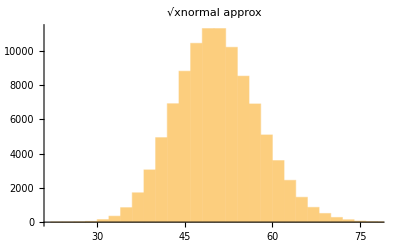

```mathematica
Histogram[x2, 30,PlotLabel->"√xnormal approx", PlotRange->{{min,max},All}]
```

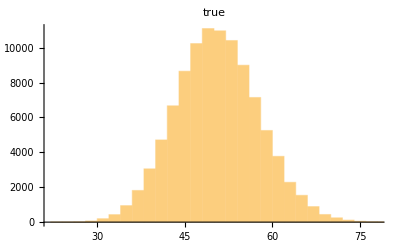

```mathematica
Histogram[y, 30, PlotLabel->"true", PlotRange->{{min,max},All}]
```

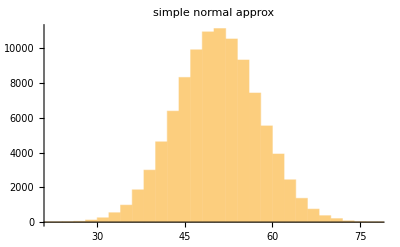

```mathematica
Histogram[z, 30, PlotLabel->"simple normal approx", PlotRange->{{min,max},All}]
```

```mathematica
PairedHistogram[y, x2, PlotLabel->"compare true vs √x normal approx" ]
```

-Graphics-

```mathematica
{EstimatedDistribution[x2, PoissonDistribution[l]], N[{Mean[x2], StandardDeviation[x2], Skewness[x2], Kurtosis[x2]}]}
```

{PoissonDistribution[49.9991],{49.9991,7.06727,0.219672,3.07505}}

```mathematica
{EstimatedDistribution[y, PoissonDistribution[l]], N[{Mean[y], StandardDeviation[y], Skewness[y], Kurtosis[y]}]}
```

{PoissonDistribution[50.0378],{50.0378,7.09715,0.135178,3.02305}}

```mathematica
{EstimatedDistribution[z, PoissonDistribution[l]], N[{Mean[z], StandardDeviation[z], Skewness[z], Kurtosis[z]}]}
```

{PoissonDistribution[50.0442],{50.0442,7.08969,-0.000381286,2.99176}}

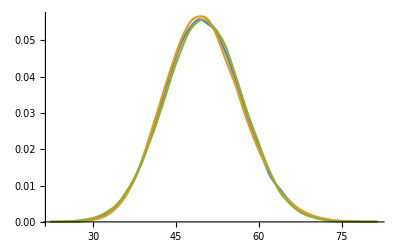

```mathematica
SmoothHistogram[{y,x2, z}, "Oversmooth"] (* jagged appearance at smaller λ because discrete distribution *)
```